# The effects of the spin down torque

## 1. The timing residuals

```mathematica
τ1∈Reals;
EllipticK[m]∈Reals;
cosα=μ1*Sin[θ0]*JacobiCN[τ,m]+μ2*Sin[θ0]*(1+δ)^(1/2)JacobiSN[τ,m]+μ3*Cos[θ0]*JacobiDN[τ,m]
```

μ3 Cos[θ0] JacobiDN[τ,m]+μ1 JacobiCN[τ,m] Sin[θ0]+√(1+δ) μ2 JacobiSN[τ,m] Sin[θ0]

```mathematica
core=Expand[cosα^2]
```

μ3^2 Cos[θ0]^2 JacobiDN[τ,m]^2+2 μ1 μ3 Cos[θ0] JacobiCN[τ,m] JacobiDN[τ,m] Sin[θ0]+2 √(1+δ) μ2 μ3 Cos[θ0] JacobiDN[τ,m] JacobiSN[τ,m] Sin[θ0]+μ1^2 JacobiCN[τ,m]^2 Sin[θ0]^2+2 √(1+δ) μ1 μ2 JacobiCN[τ,m] JacobiSN[τ,m] Sin[θ0]^2+μ2^2 JacobiSN[τ,m]^2 Sin[θ0]^2+δ μ2^2 JacobiSN[τ,m]^2 Sin[θ0]^2

```mathematica
Simplify[Assuming[m∈Reals&& m>0 && m<1&&τ∈Reals&&τ>0,Integrate[JacobiDN[τ,m]^2,τ]]]
```

(EllipticE[JacobiAmplitude[τ,m],m] JacobiDN[τ,m])/(√(1-m JacobiSN[τ,m]^2))

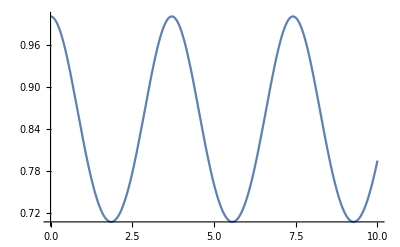

-Graphics-

```mathematica
Plot[√(1-0.5 JacobiSN[τ,0.5]^2),{τ,0,10}]
Plot[JacobiDN[τ,0.5],{τ,0,10}]
```

```mathematica
sol1=Simplify[Integrate[μ3^2 Cos[θ0]^2 JacobiDN[τ,m]^2,τ]]
```

(μ3^2 Cos[θ0]^2 EllipticE[JacobiAmplitude[τ,m],m] JacobiDN[τ,m])/(√(1-m JacobiSN[τ,m]^2))

```mathematica
sol1=μ3^2 Cos[θ0]^2 EllipticE[JacobiAmplitude[τ,m],m]
```

μ3^2 Cos[θ0]^2 EllipticE[JacobiAmplitude[τ,m],m]

```mathematica
sol2=Simplify[Integrate[2 μ1 μ3 Cos[θ0] JacobiCN[τ,m] JacobiDN[τ,m] Sin[θ0],τ]]
```

μ1 μ3 JacobiSN[τ,m] Sin[2 θ0]

```mathematica
sol3=Simplify[Integrate[2 √(1+δ) μ2 μ3 Cos[θ0] JacobiDN[τ,m] JacobiSN[τ,m] Sin[θ0],τ]]
```

-√(1+δ) μ2 μ3 JacobiCN[τ,m] Sin[2 θ0]

```mathematica
sol4=Simplify[Integrate[μ1^2 JacobiCN[τ,m]^2 Sin[θ0]^2,τ]]
```

μ1^2 (τ-τ/m+(EllipticE[JacobiAmplitude[τ,m],m] (-1+1/m+JacobiCN[τ,m]^2))/(JacobiDN[τ,m] √(1-m JacobiSN[τ,m]^2))) Sin[θ0]^2

```mathematica
sol4=μ1^2 (τ-τ/m+EllipticE[JacobiAmplitude[τ,m],m]/m) Sin[θ0]^2
```

μ1^2 (τ-τ/m+EllipticE[JacobiAmplitude[τ,m],m]/m) Sin[θ0]^2

```mathematica
sol5=Simplify[Integrate[2 √(1+δ) μ1 μ2 JacobiCN[τ,m] JacobiSN[τ,m] Sin[θ0]^2,τ]]
```

-(2 √(1+δ) μ1 μ2 JacobiDN[τ,m] Sin[θ0]^2)/m

```mathematica
Simplify[Integrate[μ2^2 JacobiSN[τ,m]^2 Sin[θ0]^2,τ]]
```

(μ2^2 (τ JacobiDN[τ,m]-EllipticE[JacobiAmplitude[τ,m],m] √(1-m JacobiSN[τ,m]^2)) Sin[θ0]^2)/(m JacobiDN[τ,m])

```mathematica
sol6=(μ2^2 (τ -EllipticE[JacobiAmplitude[τ,m],m] ) Sin[θ0]^2)/m
```

(μ2^2 (τ-EllipticE[JacobiAmplitude[τ,m],m]) Sin[θ0]^2)/m

```mathematica
sol7=δ*sol6
```

(δ μ2^2 (τ-EllipticE[JacobiAmplitude[τ,m],m]) Sin[θ0]^2)/m

```mathematica
sol=Simplify[sol1+sol2+sol3+sol4+sol5+sol6+sol7]
```

1/m(m μ3^2 Cos[θ0]^2 EllipticE[JacobiAmplitude[τ,m],m]+μ2^2 (τ-EllipticE[JacobiAmplitude[τ,m],m]) Sin[θ0]^2+δ μ2^2 (τ-EllipticE[JacobiAmplitude[τ,m],m]) Sin[θ0]^2+μ1^2 ((-1+m) τ+EllipticE[JacobiAmplitude[τ,m],m]) Sin[θ0]^2-2 √(1+δ) μ1 μ2 JacobiDN[τ,m] Sin[θ0]^2-m √(1+δ) μ2 μ3 JacobiCN[τ,m] Sin[2 θ0]+m μ1 μ3 JacobiSN[τ,m] Sin[2 θ0])

```mathematica
s1=Simplify[Coefficient[sol,EllipticE[JacobiAmplitude[τ,m],m]]]EllipticE[JacobiAmplitude[τ,m],m]
```

EllipticE[JacobiAmplitude[τ,m],m] (μ3^2 Cos[θ0]^2+((μ1^2-(1+δ) μ2^2) Sin[θ0]^2)/m)

```mathematica
s2=Simplify[Coefficient[sol,τ]]τ
```

(((-1+m) μ1^2+(1+δ) μ2^2) τ Sin[θ0]^2)/m

```mathematica
s3=Simplify[Coefficient[sol,JacobiDN[τ,m]]]JacobiDN[τ,m]
```

-(2 √(1+δ) μ1 μ2 JacobiDN[τ,m] Sin[θ0]^2)/m

```mathematica
s4=Simplify[Coefficient[sol,JacobiSN[τ,m]]]JacobiSN[τ,m]
```

μ1 μ3 JacobiSN[τ,m] Sin[2 θ0]

```mathematica
s5=Simplify[Coefficient[sol,JacobiCN[τ,m]]]JacobiCN[τ,m]
```

-√(1+δ) μ2 μ3 JacobiCN[τ,m] Sin[2 θ0]

```mathematica
Simplify[sol-s1-s2-s3-s4-s5]
```

0

```mathematica
s6=-sol/.{τ-> 0}
```

-(-2 √(1+δ) μ1 μ2 Sin[θ0]^2-m √(1+δ) μ2 μ3 Sin[2 θ0])/m

```mathematica
s1
```

EllipticE[JacobiAmplitude[τ,m],m] (μ3^2 Cos[θ0]^2+((μ1^2-(1+δ) μ2^2) Sin[θ0]^2)/m)

```mathematica
s1
```

EllipticE[JacobiAmplitude[τ,m],m] (μ3^2 Cos[θ0]^2+((μ1^2-(1+δ) μ2^2) Sin[θ0]^2)/m)

```mathematica
s2
```

(((-1+m) μ1^2+(1+δ) μ2^2) τ Sin[θ0]^2)/m

```mathematica
s3
```

-(2 √(1+δ) μ1 μ2 JacobiDN[τ,m] Sin[θ0]^2)/m

```mathematica
s4
```

μ1 μ3 JacobiSN[τ,m] Sin[2 θ0]

```mathematica
s5
```

-√(1+δ) μ2 μ3 JacobiCN[τ,m] Sin[2 θ0]

```mathematica
s6
```

-(-2 √(1+δ) μ1 μ2 Sin[θ0]^2-m √(1+δ) μ2 μ3 Sin[2 θ0])/m